```mathematica
Z1 = 1 + (1 - a^2)^(1/3) ( (1 + a)^(1/3) + (1 - a)^(1/3) );
Z2 = Sqrt[ 3 a^2 + Z1^2 ];
ru = 3 + Z2 - Sqrt[ (3 - Z1)(3 + Z1 + 2 Z2) ];
rl = 3 + Z2 + Sqrt[ (3 - Z1)(3 + Z1 + 2 Z2) ];
myr=If[a>0,ru,rl];
l = ( Sqrt[r] (r^2 - 2 a Sqrt[r] + a^2))/(r (r^2 - 3 r + 2 a Sqrt[r])^(1/2) )//.{r->myr};
lu = ( Sqrt[r] (r^2 - 2 a Sqrt[r] + a^2))/(r (r^2 - 3 r + 2 a Sqrt[r])^(1/2) )//.{r->ru};
```

```mathematica
lu//.{a->0}
```

2 √3

```mathematica
Lms=lu;
AA=1+(a/r)^2+2*a^2/r^3
BB=1+a/r^(3/2)
CC=1-3/r+2*a/r^(3/2)
DD=1-2/r+(a/r)^2
EE=1+4*(a/r)^2-4*a^2/r^3+3*a^4/r^4
FF=1-2*a/r^(3/2)+a^2/r^2
GG=1-2/r+a/r^(3/2)
(*JJ=Exp[+3/2*Integrate[(BB*CC)^(-1)*FF*r^(-2),{r,rp,Infinity}]]//.{rp->r}*)
LL=FF/CC^(1/2)-Lms/(M*r)^(1/2)
(*QQ=LL-3/(2*r^(1/2))*JJ*Integrate[FF*LL/(BB**)
WoMdot=(1/(2*Pi))*(M/r^3)^(1/2)*CC^(1/2)*LL/(BB*DD);
```

1+(2 a^2)/r^3+a^2/r^2

1+a/r^(3/2)

1+(2 a)/r^(3/2)-3/r

1+a^2/r^2-2/r

1+(3 a^4)/r^4-(4 a^2)/r^3+(4 a^2)/r^2

1+a^2/r^2-(2 a)/r^(3/2)

1+a/r^(3/2)-2/r

(1+a^2/r^2-(2 a)/r^(3/2))/(√(1+(2 a)/r^(3/2)-3/r))-(a^2-2 a √(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))+(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))^2)/(√(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)))) √(2 a √(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))-3 (3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))+(3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2))))^2) √(M r))

```mathematica
fs=FullSimplify[WoMdot//.{M->1,a->0},{r>1}]
```

(-2 √3 √(-3+r)+r)/(2 π (-2+r) r^(3/2))

```mathematica
sols=Solve[D[fs,r]==0,r]
N[sols]
mysol=N[sols[[2,1,2]]];
fs//.{r->mysol}
```

{{r→6},{r→59/12+1/2 √(4027/108+1/27 (9548416-31104 √5419)^(1/3)+4/27 (2 (74597+243 √5419))^(1/3))+1/2 √(4027/54-1/27 (9548416-31104 √5419)^(1/3)-4/27 (2 (74597+243 √5419))^(1/3)+15449/(36 √(4027/108+1/27 (9548416-31104 √5419)^(1/3)+4/27 (2 (74597+243 √5419))^(1/3))))}}

{{r→6.},{r→13.9838}}

0.00063573

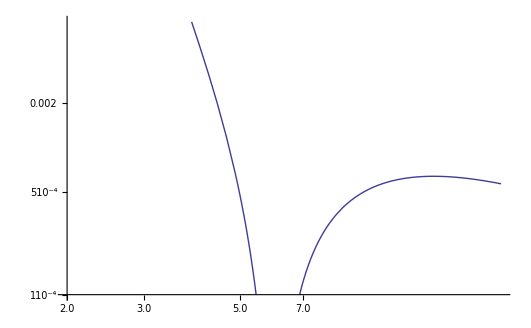

```mathematica
LogLogPlot[fs,{r,2,20},PlotRange->{10^(-4),7.1*10^(-3)}]
```

```mathematica
soly=Solve[y^3-3*y+2*a==0,y]
soly//.{a->0.0}
y1=soly[[2,1,2]]
y2=soly[[3,1,2]]
y3=soly[[1,1,2]]
yms=myr^(1/2)
```

{{y→1/((-a+√(-1+a^2))^(1/3))+(-a+√(-1+a^2))^(1/3)},{y→-(1+ⅈ √3)/(2 (-a+√(-1+a^2))^(1/3))-1/2 (1-ⅈ √3) (-a+√(-1+a^2))^(1/3)},{y→-(1-ⅈ √3)/(2 (-a+√(-1+a^2))^(1/3))-1/2 (1+ⅈ √3) (-a+√(-1+a^2))^(1/3)}}

{{y→1.73205+0. ⅈ},{y→-1.73205+0. ⅈ},{y→-2.07191×10^-16+0. ⅈ}}

-(1+ⅈ √3)/(2 (-a+√(-1+a^2))^(1/3))-1/2 (1-ⅈ √3) (-a+√(-1+a^2))^(1/3)

-(1-ⅈ √3)/(2 (-a+√(-1+a^2))^(1/3))-1/2 (1+ⅈ √3) (-a+√(-1+a^2))^(1/3)

1/((-a+√(-1+a^2))^(1/3))+(-a+√(-1+a^2))^(1/3)

√If[a>0,ru,rl]

```mathematica
omegak=1/(x^(3/2)+a);
Ax=1-2/x+a^2/x^2;
Bx=1-3/x+2*a/x^(3/2);
y=x^(1/2);
Cx=1-yms/y-3*a/(2*y)*Log[y/yms]-3*(y1-a)^2/(y*y1*(y1-y2)*(y1-y3))*Log[(y-y1)/(yms-y1)]-3*(y2-a)^2/(y*y2*(y2-y1)*(y2-y3))*Log[(y-y2)/(yms-y2)]-3*(y3-a)^2/(y*y3*(y3-y1)*(y3-y2))*Log[(y-y3)/(yms-y3)];
Rt=Cx/Ax;
WOMdotKrolik=omegak/(2*Pi)*Rt;
```

```mathematica
fsk=WOMdotKrolik//.{a->0.0}
fsk=Chop[fsk//.{r->x},10^(-14)]
```

1/(2 π (0.+r^(3/2)) (1+0./x^2-2/x))(1-2.44949/(√x)-((0.866025+0. ⅈ) Log[(1.39385+0. ⅈ) ((-1.73205+0. ⅈ)+√x)])/(√x)-((2.07191×10^-16+0. ⅈ) Log[(0.408248+0. ⅈ) ((2.07191×10^-16+0. ⅈ)+√x)])/(√x)+((0.866025+0. ⅈ) Log[(0.239146+0. ⅈ) ((1.73205+0. ⅈ)+√x)])/(√x)+(0. Log[0.408248 √x])/(√x))

(1-2.44949/(√x)-(0.866025 Log[1.39385 (-1.73205+√x)])/(√x)+(0.866025 Log[0.239146 (1.73205+√x)])/(√x))/(2 π (1-2/x) x^(3/2))

```mathematica
solk=FindRoot[D[fsk,x]==0.0,{x,13}][[1,2]]
```

13.8904

```mathematica
fsk//.{x->solk}
```

0.000600054

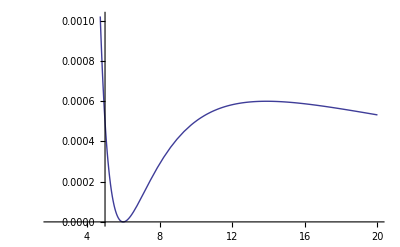

```mathematica
Plot[fsk,{x,2,20}]
```

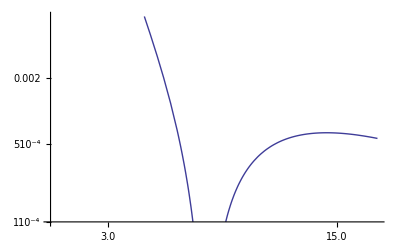

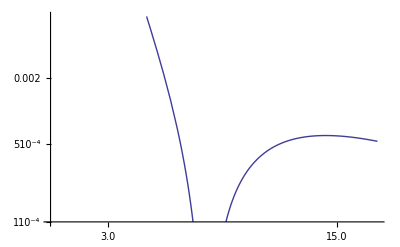

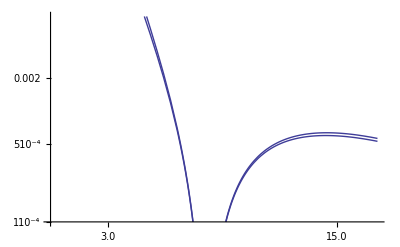

```mathematica
p1=LogLogPlot[fs,{r,2,20},PlotRange->{10^(-4),7.1*10^(-3)}]
p2=LogLogPlot[fsk,{x,2,20},PlotRange->{10^(-4),7.1*10^(-3)}]
Show[{p1,p2}]
```